```mathematica
𝕩3={ρ,z,φ};
dim3=Length[𝕩3];
f[ρ,z]=ρ^2 + (z-d)^2 - r^2;
sd=Table[D[f[ρ,z],𝕩3[[i]]],{i,1,3}]
γc={{1,0,0},{0,1,0},{0,0,ρ^2}};
γcinv=Inverse[γc];su=Table[Sum[γcinv[[i,j]]sd[[j]],{j,1,3}],{i,1,3}];
α=Sqrt[Simplify[Sum[sd[[i]]su[[i]],{i,1,3}]]];
su=su/α;
sd=sd/α;
Simplify[Sum[sd[[i]]su[[i]],{i,1,3}]]
Γγc=Simplify[Table[Sum[1/2 γcinv[[i,l]] (D[γc[[k,l]],𝕩3[[j]]]+D[γc[[j,l]],𝕩3[[k]]]-D[γc[[j,k]],𝕩3[[l]]]),{l,1,dim3}],{i,dim3},{j,dim3},{k,dim3}]];
ω[ρ_,z_]=1-((ρ^2 + z^2)/Rp^2);
```

{2 ρ,2 (-d+z),0}

1

```mathematica
Ω[ρ,z]=ω[ρ,z]/ϕ[ρ,z]^2;
```

```mathematica
Ds=Simplify[Sum[D[su[[i]],𝕩3[[i]]],{i,1,dim3}] + Sum[Γγc[[i,i,j]]su[[j]],{i,1,dim3},{j,1,dim3}]];sΩ=Simplify[Sum[su[[i]] D[Ω[ρ,z],𝕩3[[i]]],{i,1,dim3}]];
h1=Simplify[1/4(ω[ρ,z]Ds - 2Sum[su[[i]]D[ω[ρ,z],𝕩3[[i]]],{i,1,dim3}])]
h2=1/6 ktr
Add={{(3 Pz1 (d1-z)^2 z Sqrt[d1^2-2 d1 z+z^2+ρ^2]-2 c1 (d1^4-4 d1^3 z+z^4-z^2 ρ^2-2 ρ^4+d1^2 (6 z^2-ρ^2)+d1 (-4 z^3+2 z ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2))+(3 Pz2 (d2-z)^2 z Sqrt[d2^2-2 d2 z+z^2+ρ^2]-2 c2 (d2^4-4 d2^3 z+z^4-z^2 ρ^2-2 ρ^4+d2^2 (6 z^2-ρ^2)+d2 (-4 z^3+2 z ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2)),-((3 ρ (-2 c1 z (d1^2-2 d1 z+z^2+ρ^2)+Pz1 Sqrt[d1^2-2 d1 z+z^2+ρ^2] (d1^2-2 d1 z+2 z^2+ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2)))-(3 ρ (-2 c2 z (d2^2-2 d2 z+z^2+ρ^2)+Pz2 Sqrt[d2^2-2 d2 z+z^2+ρ^2] (d2^2-2 d2 z+2 z^2+ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2)),(3 Sz1 ρ^3)/(d1^2-2 d1 z+z^2+ρ^2)^(5/2)+(3 Sz2 ρ^3)/(d2^2-2 d2 z+z^2+ρ^2)^(5/2)},{-((3 ρ (-2 c1 z (d1^2-2 d1 z+z^2+ρ^2)+Pz1 Sqrt[d1^2-2 d1 z+z^2+ρ^2] (d1^2-2 d1 z+2 z^2+ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2)))-(3 ρ (-2 c2 z (d2^2-2 d2 z+z^2+ρ^2)+Pz2 Sqrt[d2^2-2 d2 z+z^2+ρ^2] (d2^2-2 d2 z+2 z^2+ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2)),-((c1 (d1^2-2 d1 z-2 z^2+ρ^2))/((d1-z)^2+ρ^2)^(5/2))-(c2 (d2^2-2 d2 z-2 z^2+ρ^2))/((d2-z)^2+ρ^2)^(5/2)-(3 Pz1 z (d1^2-2 d1 z+2 z^2+ρ^2))/(2 (d1^2-2 d1 z+z^2+ρ^2)^3)-(3 Pz2 z (d2^2-2 d2 z+2 z^2+ρ^2))/(2 (d2^2-2 d2 z+z^2+ρ^2)^3),(3 Sz1 z ρ^2)/(d1^2-2 d1 z+z^2+ρ^2)^(5/2)+(3 Sz2 z ρ^2)/(d2^2-2 d2 z+z^2+ρ^2)^(5/2)},{(3 Sz1 ρ^3)/(d1^2-2 d1 z+z^2+ρ^2)^(5/2)+(3 Sz2 ρ^3)/(d2^2-2 d2 z+z^2+ρ^2)^(5/2),(3 Sz1 z ρ^2)/(d1^2-2 d1 z+z^2+ρ^2)^(5/2)+(3 Sz2 z ρ^2)/(d2^2-2 d2 z+z^2+ρ^2)^(5/2),1/2 ρ^2 ((3 Pz1 z)/(d1^2-2 d1 z+z^2+ρ^2)^2-(2 c1)/(d1^2-2 d1 z+z^2+ρ^2)^(3/2))+1/2 ρ^2 ((3 Pz2 z)/(d2^2-2 d2 z+z^2+ρ^2)^2-(2 c2)/(d2^2-2 d2 z+z^2+ρ^2)^(3/2))}};
h3=-ω[ρ,z]^3/4 Sum[su[[i]]su[[j]]Add[[i,j]],{i,1,dim3},{j,1,dim3}];
hh33=-1/4 Sum[su[[i]]su[[j]]Add[[i,j]],{i,1,dim3},{j,1,dim3}];
ssA=Sum[su[[i]]su[[j]]Add[[i,j]],{i,1,dim3},{j,1,dim3}];
```

(Rp^2-2 d z+z^2+ρ^2)/(2 Rp^2 √(d^2-2 d z+z^2+ρ^2))

ktr/6

```mathematica
CForm[h2/.ρ->rho]/.Power->pow
```

ktr/6.

```mathematica
su
```

{ρ/(√((d-z)^2+ρ^2)),(-d+z)/(√((d-z)^2+ρ^2)),0}

```mathematica
Θp = 2/3 ktr-Ω[ρ,z]^3 ssA+(Ω[ρ,z] Ds-2 sΩ)
```

(2 ktr)/3-1/ϕ[ρ,z]^6(1-(z^2+ρ^2)/Rp^2)^3 (((-d+z)^2 (-(c1 (d1^2-2 d1 z-2 z^2+ρ^2))/(((d1-z)^2+ρ^2)^(5/2))-(c2 (d2^2-2 d2 z-2 z^2+ρ^2))/(((d2-z)^2+ρ^2)^(5/2))-(3 Pz1 z (d1^2-2 d1 z+2 z^2+ρ^2))/(2 (d1^2-2 d1 z+z^2+ρ^2)^3)-(3 Pz2 z (d2^2-2 d2 z+2 z^2+ρ^2))/(2 (d2^2-2 d2 z+z^2+ρ^2)^3)))/((d-z)^2+ρ^2)+1/((d-z)^2+ρ^2)2 (-d+z) ρ (-(3 ρ (-2 c1 z (d1^2-2 d1 z+z^2+ρ^2)+Pz1 √(d1^2-2 d1 z+z^2+ρ^2) (d1^2-2 d1 z+2 z^2+ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2))-(3 ρ (-2 c2 z (d2^2-2 d2 z+z^2+ρ^2)+Pz2 √(d2^2-2 d2 z+z^2+ρ^2) (d2^2-2 d2 z+2 z^2+ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2)))+1/((d-z)^2+ρ^2)ρ^2 ((3 Pz1 (d1-z)^2 z √(d1^2-2 d1 z+z^2+ρ^2)-2 c1 (d1^4-4 d1^3 z+z^4-z^2 ρ^2-2 ρ^4+d1^2 (6 z^2-ρ^2)+d1 (-4 z^3+2 z ρ^2)))/(2 (d1^2-2 d1 z+z^2+ρ^2)^(7/2))+(3 Pz2 (d2-z)^2 z √(d2^2-2 d2 z+z^2+ρ^2)-2 c2 (d2^4-4 d2^3 z+z^4-z^2 ρ^2-2 ρ^4+d2^2 (6 z^2-ρ^2)+d2 (-4 z^3+2 z ρ^2)))/(2 (d2^2-2 d2 z+z^2+ρ^2)^(7/2))))+(2 (1-(z^2+ρ^2)/Rp^2))/(√(d^2-2 d z+z^2+ρ^2) ϕ[ρ,z]^2)-(4 ((d z-z^2-ρ^2) ϕ[ρ,z]-(Rp^2-z^2-ρ^2) ((-d+z) ϕ^(0,1)[ρ,z]+ρ ϕ^(1,0)[ρ,z])))/(Rp^2 √(d^2-2 d z+z^2+ρ^2) ϕ[ρ,z]^3)

```mathematica
CForm[Θp/.ϕ[ρ,z]->phi/.Derivative[1,0][ϕ][ρ,z]->dphidrho/.Derivative[0,1][ϕ][ρ,z]->dphidz/.ρ->rho]/.Power->pow
```

(2*ktr)/3. - 4*pow(phi,-3)*pow(Rp,-2)*(phi*(d*z - pow(rho,2) - pow(z,2)) - 
      (dphidrho*rho + dphidz*(-d + z))*(-pow(rho,2) + pow(Rp,2) - pow(z,2)))*
    pow(-2*d*z + pow(d,2) + pow(rho,2) + pow(z,2),-0.5) + 
   2*pow(phi,-2)*(1 - pow(Rp,-2)*(pow(rho,2) + pow(z,2)))*pow(-2*d*z + pow(d,2) + pow(rho,2) + pow(z,2),-0.5) - 
   pow(phi,-6)*(pow(-d + z,2)*pow(pow(rho,2) + pow(d - z,2),-1)*
       (-(c1*(-2*d1*z + pow(d1,2) + pow(rho,2) - 2*pow(z,2))*pow(pow(rho,2) + pow(d1 - z,2),-2.5)) - 
         c2*(-2*d2*z + pow(d2,2) + pow(rho,2) - 2*pow(z,2))*pow(pow(rho,2) + pow(d2 - z,2),-2.5) - 
         (3*Pz1*z*(-2*d1*z + pow(d1,2) + pow(rho,2) + 2*pow(z,2))*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3))/2. - 
         (3*Pz2*z*(-2*d2*z + pow(d2,2) + pow(rho,2) + 2*pow(z,2))*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3))/2.) + 
      pow(rho,2)*pow(pow(rho,2) + pow(d - z,2),-1)*
       ((pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3.5)*
            (-2*c1*(-4*z*pow(d1,3) + pow(d1,4) - 2*pow(rho,4) - pow(rho,2)*pow(z,2) + pow(d1,2)*(-pow(rho,2) + 6*pow(z,2)) + 
                 d1*(2*z*pow(rho,2) - 4*pow(z,3)) + pow(z,4)) + 
              3*Pz1*z*pow(d1 - z,2)*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),0.5)))/2. + 
         (pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3.5)*
            (-2*c2*(-4*z*pow(d2,3) + pow(d2,4) - 2*pow(rho,4) - pow(rho,2)*pow(z,2) + pow(d2,2)*(-pow(rho,2) + 6*pow(z,2)) + 
                 d2*(2*z*pow(rho,2) - 4*pow(z,3)) + pow(z,4)) + 
              3*Pz2*z*pow(d2 - z,2)*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),0.5)))/2.) + 
      2*rho*(-d + z)*pow(pow(rho,2) + pow(d - z,2),-1)*
       ((-3*rho*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),-3.5)*
            (-2*c1*z*(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2)) + 
              Pz1*(-2*d1*z + pow(d1,2) + pow(rho,2) + 2*pow(z,2))*pow(-2*d1*z + pow(d1,2) + pow(rho,2) + pow(z,2),0.5)))/2. - 
         (3*rho*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),-3.5)*
            (-2*c2*z*(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2)) + 
              Pz2*(-2*d2*z + pow(d2,2) + pow(rho,2) + 2*pow(z,2))*pow(-2*d2*z + pow(d2,2) + pow(rho,2) + pow(z,2),0.5)))/2.))*
    pow(1 - pow(Rp,-2)*(pow(rho,2) + pow(z,2)),3)

```mathematica
sd2={sd[[1]],sd[[2]]};
su2={su[[1]],su[[2]]};
```

```mathematica
a0=1;
Rp=10;
r1=1;
r2=1;
eta1=ArcSinh[a0/r1];
eta2=-ArcSinh[a0/r2];
d1=Sqrt[a0^2+r1^2];
d2=-Sqrt[a0^2+r2^2];
```

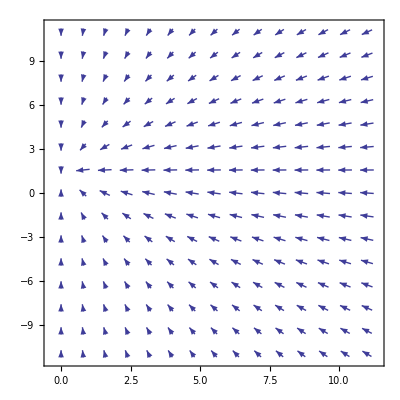

```mathematica
VectorPlot[{su2/.d->d1},{ρ,0,1.1*Rp},{z,-1.1*Rp,1.1*Rp},VectorScale->0.02]
```